# Expected value of balance indices using basis statistics

## Balance indices represented by the clade-number basis

For the eight statistics which are represented by the clade-number basis, we can use the given representations (Appendix A) and the following functions to simplify the expression for the mean. We are using the formula

to find the mean expressions, and a custom function simpHarmonic to try to simplify it using HarmonicNumbers instead of functions like PolyGamma.

```mathematica
(*Defining all of the relevant quantities for the clade number basis *)

(* Module to calculate the mean of statistic represented by clade-number basis with representation f[n,r] *)
MeanCladeStatistic[stat_,n_]:=Module[{sum,final},sum=Sum[stat[n,r]*2 n/(r (r+1)),{r,2,n-1}];
final=sum+stat[n,n];
FullSimplify[final,Assumptions->{n>3,n∈Integers}]]
```

```mathematica
(* Defining statistic representations for all statistics represented by clade-number basis *)
sackin[n_,r_] := r;
averageLeafDepth[n_,r_]:= r/n;
totalCophenetic[n_,r_]:=Piecewise[{{Binomial[r,2], r < n},{0,r == n}}];
sHat[n_,r_] :=Log[r-1];
quadraticColless[n_,r_]:= Piecewise[{{r^2, r < n}, {2n-n^2, r==n}}];
tIPL[n_,r_]:=Piecewise[{{r, r<n}, {2-n, r == n}}];
tPL[n_,r_]:=Piecewise[{{2r, r < n}, {2, r==n}}];
aVD[n_,r_]:=Piecewise[{{2r/(2n-1), r < n}, {2/(2n-1), r == n}}];
```

2 n (-1+HarmonicNumber[n])

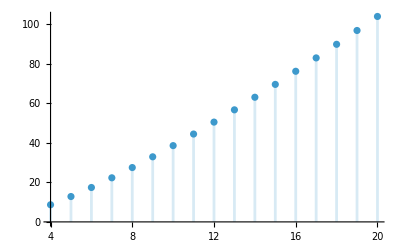

```mathematica
(* Calculating the mean in as simple of a formula as possible, for each statistic represented by clade-number basis *)
(* Sackin index *)
meanSackin = MeanCladeStatistic[sackin, n]
DiscretePlot[meanSackin, {n, 4, 20}]
```

-2+2 HarmonicNumber[n]

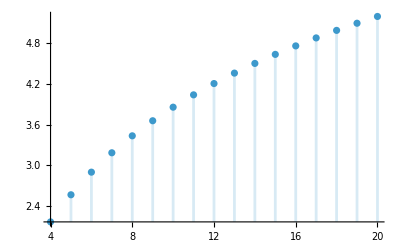

```mathematica
meanAverageLeafDepth = MeanCladeStatistic[averageLeafDepth, n]
DiscretePlot[meanAverageLeafDepth, {n, 4, 20}]
```

n (1+n-2 HarmonicNumber[n])

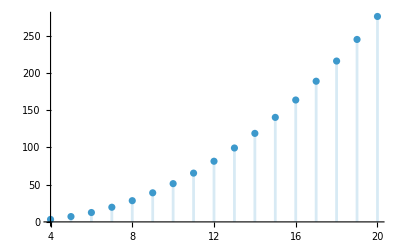

```mathematica
meanTotalCophenetic = MeanCladeStatistic[totalCophenetic,n]
DiscretePlot[meanTotalCophenetic, {n, 4, 20}]
```

Log[-1+n]+∑_(r=2)^(-1+n) (2 n Log[-1+r])/(r (1+r))

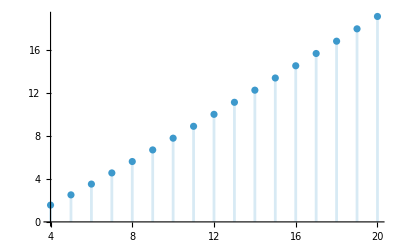

```mathematica
meanSHat = MeanCladeStatistic[sHat, n]
DiscretePlot[meanSHat, {n, 4, 20}]
```

```mathematica
meanQuadraticColless = MeanCladeStatistic[quadraticColless, n]
DiscretePlot[meanQuadraticColless, {n, 4, 20}]
```

n (1+n-2 HarmonicNumber[n])

-Graphics-

2-4 n+2 n HarmonicNumber[n]

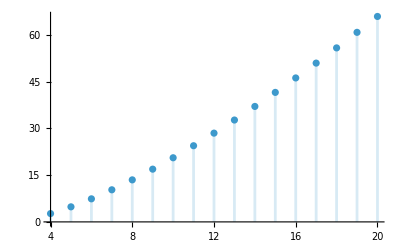

```mathematica
meanTIPL = MeanCladeStatistic[tIPL, n]
DiscretePlot[meanTIPL, {n, 4, 20}]
```

2-6 n+4 n HarmonicNumber[n]

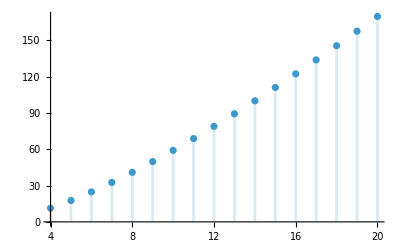

```mathematica
meanTPL = MeanCladeStatistic[tPL, n]
DiscretePlot[meanTPL, {n, 4, 20}]
```

(2-6 n+4 n HarmonicNumber[n])/(-1+2 n)

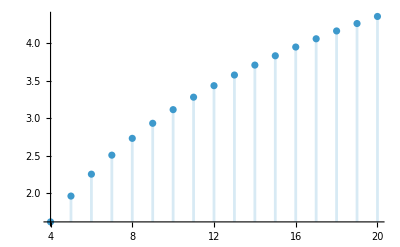

```mathematica
meanAVD = MeanCladeStatistic[aVD, n]
DiscretePlot[meanAVD, {n, 4, 20}]
```

## Balance indices represented by the daughter-number basis

Finding the mean of balance indices represented by the daughter-number basis is a bit trickier. Instead of summing over , we will first sum over all pairs  with , for , and then sum those partial sums up. Recall that the mean of a statistic  which is represented by the daughter-number basis with coefficients  is given by 

The expected daughter number  now has two cases, because  unless , in which case it is equal to . Therefore, to find the sum for a fixed value of , if  is even it will be equal to 

while if  is odd this will be equal to 

Now, splitting into the cases where  and   and separating into  even and  odd gives us our full expressions for sums, which we do out below.

```mathematica
(* Function to solve mean for statistics represented by daughter-number basis *)
(* Sum p_k(i) * stat[n, i, j] over a level set i + j = k; split into k even and k odd *)
PartialSumEvenK[stat_, n_, k_] := Simplify[Sum[stat[n,i, k-i] * 2/(k-1), {i, 1, k/2 - 1}] + stat[n, k/2, k/2] /(k-1), Assumptions->{n>3,n∈Integers, 2 <= k <= n, Mod[k, 2]==0}];
PartialSumOddK[stat_, n_,k_]:= Simplify[Sum[stat[n,i, k-i] * 2/(k-1), {i, 1, (k-1)/2 }], Assumptions->{n>3,n∈Integers, 2 <= k <= n, Mod[k, 2]==1}];

(* Now sum M(n,k) * Partial Sum over k=2,...,n, splitting into even and odd n cases. k0=2 is the default*)
MeanStatEvenN[stat_, n_] := Simplify[Sum[2n/(k(k+1)) * PartialSumEvenK[stat, n,k], {k, 2, n-2, 2}]
+ Sum[2n/(k(k+1))*PartialSumOddK[stat, n, k], {k, 3, n-1, 2}] 
+ PartialSumEvenK[stat, n, n], 
Assumptions -> {n>3,n∈Integers, Mod[n, 2]==0}];
MeanStatOddN[stat_, n_] := Simplify[Sum[2n/(k(k+1)) * PartialSumEvenK[stat, n,k], {k, 2, n-1, 2}]
+ Sum[2n/(k(k+1))*PartialSumOddK[stat, n, k], {k, 3, n-2, 2}] 
+ PartialSumOddK[stat, n, n], 
Assumptions -> {n>3,n∈Integers, Mod[n, 2]==1}];

(* Aggregate into a final function *)
(* Simplify in a way that chooses a form involving HarmonicNumber instead of PolyGamma functions *)
simpHarmonic=FullSimplify[#,ComplexityFunction->(LeafCount[#]+100Count[#,_PolyGamma,All]&)]&;

MeanDaughterStatistic[stat_, n_] := simpHarmonic[Piecewise[{{MeanStatEvenN[stat, n], Mod[n,2] == 0}, {MeanStatOddN[stat, n], Mod[n,2] == 1}}], Assumptions -> {n>3,n∈Integers}];
```

```mathematica
(* Representations of indices represented by the daughter-number basis *)
colless[n_,i_,j_]:= j-i;
correctedColless[n_,i_,j_]:=2(j-i)/(n-1)/(n-2);
i2[n_,i_,j_]:=Piecewise[{{(j-i)/((n-2)(i+j-2)), i+j > 2}, {0, i+j == 2}}];
totalI[n_,i_,j_]:=(j - Floor[(i+j)/2])/((i+j-1) - Floor[(i+j)/2]); (* 0 when i + j < 4; use modified function *)
totalIPrime[n_,i_,j_]:= Piecewise[{{((j - i)(i + j - 1))/((i + j)(i + j - 2)), Mod[i + j, 2]== 0}, {(j - i + 1)/(i + j - 1), Mod[i + j, 2] == 1}}]; (* 0 when i + j < 4; use modified function *)
rogersJ[n_,i_,j_]:=Piecewise[{{1, i != j}, {0, i == j}}];
rQIB[n_,i_,j_]:=Binomial[i,2]*Binomial[j,2];
stairs1[n_,i_,j_]:=Piecewise[{{1/(n-1), i != j}, {0, i == j}}];
stairs2[n_,i_,j_]:=i/j/(n-1);
```

Piecewise[{{n (-1+HarmonicNumber[n/2]), Mod[n,2]==0}, {1-n+n HarmonicNumber[1/2 (-1+n)], Mod[n,2]==1}, {0, True}}]

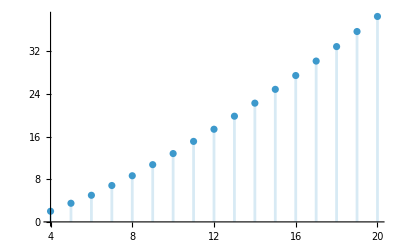

```mathematica
(* Calculating mean of each index represented by daughter-number basis *)
collessMean = MeanDaughterStatistic[colless, n]
DiscretePlot[collessMean, {n, 4, 20}]
```

Piecewise[{{(2 n (-1+HarmonicNumber[n/2]))/((-2+n) (-1+n)), Mod[n,2]==0}, {(2 (1-n+n HarmonicNumber[1/2 (-1+n)]))/((-2+n) (-1+n)), Mod[n,2]==1}, {0, True}}]

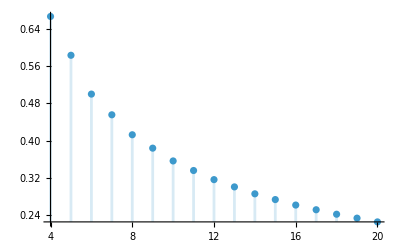

```mathematica
correctedCollessMean = MeanDaughterStatistic[correctedColless, n]
DiscretePlot[correctedCollessMean, {n, 4, 20}]
```

Piecewise[{{(n (3/(-1+n)+2 HarmonicNumber[1/2 (-3+n)]-2 HarmonicNumber[n/2]+Log[16]))/(6 (-2+n)), Mod[n,2]==0}, {(3 (1+n)+2 (-2+n) n (HarmonicNumber[1/2 (-4+n)]-HarmonicNumber[1/2 (-1+n)]+Log[4]))/(6 (-2+n)^2), Mod[n,2]==1}, {0, True}}]

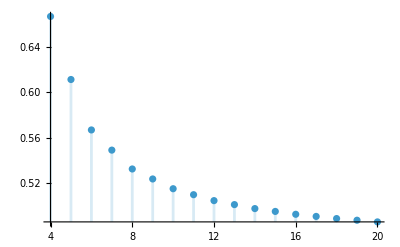

```mathematica
(*  Things did not quite work for i2 mean because sum requires i + j = k > 2, so made custom functions *)
i2G2[n_,i_,j_]:= (j - i) / (i + j - 2) / (n - 2);
MeanI2EvenN[n_]:= Simplify[Sum[2n/(k(k+1)) * PartialSumEvenK[i2G2, n,k], {k, 4, n-2, 2}]
+ Sum[2n/(k(k+1))*PartialSumOddK[i2G2, n, k], {k, 3, n-1, 2}] 
+ PartialSumEvenK[i2G2, n, n], 
Assumptions -> {n>3,n∈Integers, Mod[n, 2]==0}];
MeanI2OddN[n_]:=Simplify[Sum[2n/(k(k+1)) * PartialSumEvenK[i2G2, n,k], {k, 4, n-1, 2}]
+ Sum[2n/(k(k+1))*PartialSumOddK[i2G2, n, k], {k, 3, n-2, 2}] 
+ PartialSumOddK[i2G2, n, n], 
Assumptions -> {n>3,n∈Integers, Mod[n, 2]==1}];
i2MeanFull[n_]:=simpHarmonic[Piecewise[{{MeanI2EvenN[n], Mod[n,2]==0}, {MeanI2OddN[n], Mod[n,2]==1}}],
Assumptions -> {n>3,n∈Integers}];

i2Mean= i2MeanFull[n]
DiscretePlot[i2Mean, {n, 4, 20}]
```

```mathematica
(* By hand, made it a bit simpler *)
i2MeanSimplified = Piecewise[{{1/(6 (-2+n))n (4 (HarmonicNumber[n] - HarmonicNumber[n/2]) - 1/(-1+n)), Mod[n, 2] == 0}, {-(-3+n+4 (-2+n) n HarmonicNumber[1/2 (-1+n)]-4 (-2+n) n HarmonicNumber[-1+n])/(6 (-2+n)^2), Mod[n,2 ] == 1}}]
DiscretePlot[i2MeanSimplified, {n, 4, 20}]
```

Piecewise[{{(n (-1/(-1+n)+4 (-HarmonicNumber[n/2]+HarmonicNumber[n])))/(6 (-2+n)), Mod[n,2]==0}, {-(-3+n+4 (-2+n) n HarmonicNumber[1/2 (-1+n)]-4 (-2+n) n HarmonicNumber[-1+n])/(6 (-2+n)^2), Mod[n,2]==1}, {0, True}}]

-Graphics-

```mathematica
FullSimplify[i2Mean==i2MeanSimplified, Assumptions->{n>3,n∈Integers}]
```

True

Piecewise[{{1/2 n (2+HarmonicNumber[1/2 (-2+n)]-HarmonicNumber[1/2 (-1+n)]-Log[4]), Mod[n,2]==0}, {1/(-1+n)+n+1/2 n (HarmonicNumber[1/2 (-3+n)]-HarmonicNumber[1/2 (-2+n)]-2 Log[2]), Mod[n,2]==1}, {0, True}}]

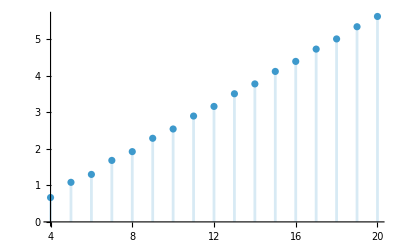

```mathematica
(* For total I, we write slightly modified functions because it is 0 for k < 4 *)
modifiedMeanStatEvenN[stat_,n_] := Simplify[Sum[2n/(k(k+1)) * PartialSumEvenK[stat, n,k], {k, 4, n-2, 2}]
+ Sum[2n/(k(k+1))*PartialSumOddK[stat, n, k], {k, 5, n-1, 2}] 
+ PartialSumEvenK[stat, n, n], 
Assumptions -> {n>5,n∈Integers, Mod[n, 2]==0}];
modifiedMeanStatOddN[stat_, n_] := Simplify[Sum[2n/(k(k+1)) * PartialSumEvenK[stat, n,k], {k, 4, n-1, 2}]
+ Sum[2n/(k(k+1))*PartialSumOddK[stat, n, k], {k, 5, n-2, 2}] 
+ PartialSumOddK[stat, n, n], 
Assumptions -> {n>5,n∈Integers, Mod[n, 2]==1}];
modifiedMeanDaughterStatistic[stat_,n_]:=simpHarmonic[Piecewise[{{modifiedMeanStatEvenN[stat, n], Mod[n,2] == 0}, {modifiedMeanStatOddN[stat, n], Mod[n,2] == 1}}], Assumptions -> {n>5,n∈Integers}];

totalIMean = modifiedMeanDaughterStatistic[totalI, n]
DiscretePlot[totalIMean, {n, 4, 20}]
```

```mathematica
(* Using the above, I simplified the formula further by hand *)
totalIMeanSimplified = Piecewise[{{n(HarmonicNumber[n/2 - 1] - HarmonicNumber[n-1] + 1), Mod[n,2]==0}, {n(HarmonicNumber[(n-1)/2] - HarmonicNumber[n-1] + 1) - 1, Mod[n,2]==1}}]
DiscretePlot[totalIMeanSimplified, {n, 4, 20}]
```

Piecewise[{{n (1+HarmonicNumber[-1+n/2]-HarmonicNumber[-1+n]), Mod[n,2]==0}, {-1+n (1+HarmonicNumber[1/2 (-1+n)]-HarmonicNumber[-1+n]), Mod[n,2]==1}, {0, True}}]

-Graphics-

```mathematica
FullSimplify[totalIMean ==totalIMeanSimplified, Assumptions->{n>3, n∈Integers}]
```

True

Piecewise[{{1/2+(5 n)/3+n HarmonicNumber[1/2 (-2+n)]-n HarmonicNumber[1/2 (-1+n)]-n Log[4], Mod[n,2]==0}, {(9+n (-7+10 n)+6 (-1+n) n (HarmonicNumber[1/2 (-3+n)]-HarmonicNumber[1/2 (-2+n)]-2 Log[2]))/(6 (-1+n)), Mod[n,2]==1}, {0, True}}]

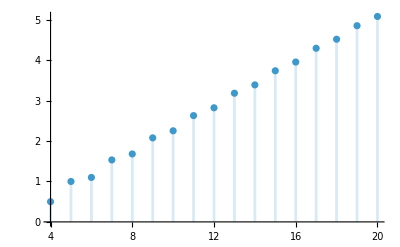

```mathematica
totalIPrimeMean = modifiedMeanDaughterStatistic[totalIPrime, n]
DiscretePlot[totalIPrimeMean, {n, 4, 20}]
```

```mathematica
(* I simplified the above formula by hand *)
totalIPrimeMeanSimplified = Piecewise[{{1/2  + n(5/3 - 2(HarmonicNumber[n - 1] - HarmonicNumber[n/2 - 1])), Mod[n,2]==0}, {1/(6 (-1+n))(9+n (-7+10 n)+12 (-1+n) n (HarmonicNumber[1/2 (-3+n)]-HarmonicNumber[-2+n])), Mod[n,2]==1}}]
DiscretePlot[totalIPrimeMeanSimplified, {n, 4, 20}]
```

Piecewise[{{1/2+n (5/3-2 (-HarmonicNumber[-1+n/2]+HarmonicNumber[-1+n])), Mod[n,2]==0}, {(9+n (-7+10 n)+12 (-1+n) n (HarmonicNumber[1/2 (-3+n)]-HarmonicNumber[-2+n]))/(6 (-1+n)), Mod[n,2]==1}, {0, True}}]

-Graphics-

```mathematica
FullSimplify[totalIPrimeMean == totalIPrimeMeanSimplified, Assumptions->{n>3,n∈Integers}]
```

True

Piecewise[{{n (2-2/(-1+n)-HarmonicNumber[1/2 (-3+n)]+HarmonicNumber[1/2 (-2+n)]-Log[4]), Mod[n,2]==0}, {-2-n HarmonicNumber[1/2 (-2+n)]+n HarmonicNumber[1/2 (-1+n)]-n (-2+Log[4]), Mod[n,2]==1}, {0, True}}]

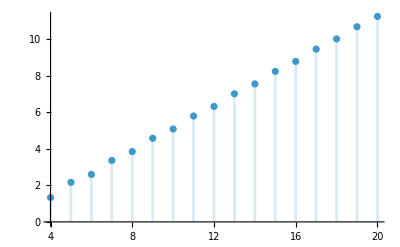

```mathematica
rogersJMean = MeanDaughterStatistic[rogersJ, n]
DiscretePlot[rogersJMean, {n, 4, 20}]
```

```mathematica
(* Computed simplified equation by hand *)
rogersJMeanSimplified = Piecewise[{{2n(HarmonicNumber[n/2 - 1] - HarmonicNumber[n-1] + 1), Mod[n,2]==0},{2n(HarmonicNumber[(n-1)/2] - HarmonicNumber[n-1] + 1) - 2, Mod[n,2]==1}}]
DiscretePlot[rogersJMeanSimplified, {n, 4, 20}]
```

Piecewise[{{2 n (1+HarmonicNumber[-1+n/2]-HarmonicNumber[-1+n]), Mod[n,2]==0}, {-2+2 n (1+HarmonicNumber[1/2 (-1+n)]-HarmonicNumber[-1+n]), Mod[n,2]==1}, {0, True}}]

-Graphics-

```mathematica
FullSimplify[rogersJMean==rogersJMeanSimplified, Assumptions->{n>3, n∈Integers}]
```

True

Piecewise[{{1/72 (-3+n) (-2+n) (-1+n) n, Mod[n,2]==0||Mod[n,2]==1}, {0, True}}]

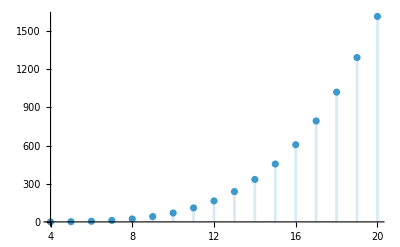

```mathematica
rQIBMean = MeanDaughterStatistic[rQIB, n]
DiscretePlot[rQIBMean, {n, 4, 20}]
```

Piecewise[{{(n (-4-(-1+n) HarmonicNumber[1/2 (-3+n)]+(-1+n) HarmonicNumber[1/2 (-2+n)]-n (-2+Log[4])+Log[4]))/(-1+n)^2, Mod[n,2]==0}, {(-2-n HarmonicNumber[1/2 (-2+n)]+n HarmonicNumber[1/2 (-1+n)]-n (-2+Log[4]))/(-1+n), Mod[n,2]==1}, {0, True}}]

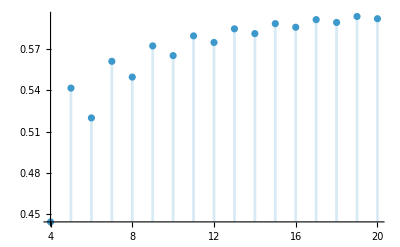

```mathematica
stairs1Mean = MeanDaughterStatistic[stairs1, n]
DiscretePlot[stairs1Mean, {n, 4, 20}]
```

```mathematica
(* Because stairs1 is just RogersJ / (n-1), we can readily use that representation for this index *)
stairs1MeanSimplified = PiecewiseExpand[1/(n-1) * rogersJMeanSimplified]
DiscretePlot[stairs1MeanSimplified, {n, 4, 20}]
```

Piecewise[{{(2 n (1+HarmonicNumber[-1+n/2]-HarmonicNumber[-1+n]))/(-1+n), Mod[n,2]==0}, {(-2+2 n (1+HarmonicNumber[1/2 (-1+n)]-HarmonicNumber[-1+n]))/(-1+n), Mod[n,2]==1}, {0, True}}]

-Graphics-

```mathematica
FullSimplify[stairs1Mean == stairs1MeanSimplified, Assumptions->{n>3,n∈Integers}]
```

True

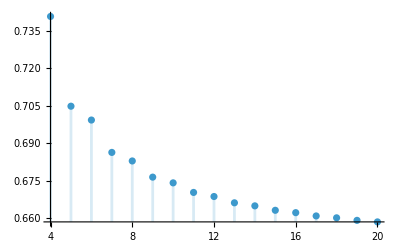

```mathematica
stairs2[n_,i_,j_]:= i / j / ( n - 1);
stairs2MeanNaive[n_]:= MeanDaughterStatistic[stairs2, n]
DiscretePlot[stairs2MeanNaive[n], {n, 4, 20}]
```

```mathematica
(* Actually compute the partial sums for stairs2 *)
PartialSumEvenK[stairs2, n, k]
```

(1-2 [k/2])/((-1+k) (-1+n))

```mathematica
PartialSumOddK[stairs2, n, k]
```

-(2 [(1+k)/2])/((-1+k) (-1+n))

```mathematica
(* Let's uncover what these DifferenceRoot expressions are *)
```

```mathematica
dr1 =  [k/2];
val1 = Table[{k,dr1}, {k, 2, 20, 2}]
fun1 = FindSequenceFunction[val1]
```

{{2,0},{4,-1/3},{6,-7/10},{8,-113/105},{10,-367/252},{12,-4247/2310},{14,-57191/25740},{16,-23477/9009},{18,-407117/136136},{20,-39288727/11639628}}

-#1/2+(EulerGamma #1)/2+1/2 PolyGamma[0,3/2] #1-1/2 PolyGamma[0,1/2+#1/2] #1+1/2 PolyGamma[0,1+#1/2] #1&

```mathematica
f1[k_]:= simpHarmonic[fun1[k]]
f1[k]
```

-1/2 k (-1+HarmonicNumber[1/2 (-1+k)]-HarmonicNumber[k/2]+Log[4])

```mathematica
Max[Table[{Abs[f1[k] - dr1]}, {k, 2, 200, 2}]]
```

0

```mathematica
f1simp[k_]:= -k / 2(2(HarmonicNumber[k] - HarmonicNumber[k / 2])  - 1);
```

```mathematica
FullSimplify[f1[k]== f1simp[k], Assumptions->k∈Integers && k >=2 && Mod[k,2]==0]
```

True

```mathematica
(* Great, we have a closed-form equation for the first one. Now the second *)
```

```mathematica
dr2 = [(1+k)/2];
val2 = Table[{k, dr2}, {k, 3, 21, 2}]
fun2 = FindSequenceFunction[val2]
```

{{3,-1/2},{5,-11/12},{7,-79/60},{9,-479/280},{11,-5297/2520},{13,-69071/27720},{15,-69203/24024},{17,-471181/144144},{19,-8960447/2450448},{21,-44831407/11085360}}

1/2 (-1+EulerGamma+PolyGamma[0,3/2]-PolyGamma[0,1/2+1/2 (-1+#1)]+PolyGamma[0,1+1/2 (-1+#1)]+EulerGamma (-1+#1)+PolyGamma[0,3/2] (-1+#1)-PolyGamma[0,1/2+1/2 (-1+#1)] (-1+#1)+PolyGamma[0,1+1/2 (-1+#1)] (-1+#1)-#1)&

```mathematica
f2[k_]:=simpHarmonic[fun2[k]]
f2[k]
```

1/2 (-1+k-k (HarmonicNumber[1/2 (-2+k)]-HarmonicNumber[1/2 (-1+k)]+Log[4]))

```mathematica
f2simp[k_]:=-1/2 - k/2(2 (HarmonicNumber[k - 1] - HarmonicNumber[(k-1)/2]) - 1);
FullSimplify[f2[k] == f2simp[k], Assumptions->k∈Integers && k >=3 && Mod[k,2]==1]
```

True

```mathematica
(* Now we are ready to construct a function that simplifies the overall formula *)
```

```mathematica
evenTerm[n_,k_]:=(1-2 f1simp[k])/((-1+k) (-1 + n));
oddTerm[n_,k_]:= -(2 f2simp[k])/((-1+k) (-1 + n));
```

```mathematica
Simplify[evenTerm[n,k]]
Simplify[oddTerm[n,k]]
```

(1-k-2 k HarmonicNumber[k/2]+2 k HarmonicNumber[k])/((-1+k) (-1+n))

(1-k-2 k HarmonicNumber[1/2 (-1+k)]+2 k HarmonicNumber[-1+k])/((-1+k) (-1+n))

```mathematica
stairs2MeanEvenN[n_] := Simplify[Sum[2n/(k(k+1)) *evenTerm[n,k], {k, 2, n-2, 2}]
+ Sum[2n/(k(k+1))*oddTerm[n,k], {k, 3, n-1, 2}] 
+ evenTerm[n,n], 
Assumptions -> {n>3,n∈Integers, Mod[n, 2]==0}];
stairs2MeanOddN[n_] := Simplify[Sum[2n/(k(k+1)) * evenTerm[n,k], {k, 2, n-1, 2}]
+ Sum[2n/(k(k+1))*oddTerm[n,k], {k, 3, n-2, 2}] 
+oddTerm[n,n], 
Assumptions -> {n>3,n∈Integers, Mod[n, 2]==1}];

(* Aggregate into a final function *)
Clear[stairs2Mean];
stairs2Mean[ n_] := simpHarmonic[Piecewise[{{stairs2MeanEvenN[n], Mod[n,2] == 0}, {stairs2MeanOddN[n], Mod[n,2] == 1}}], Assumptions->n∈Integers && n > 3];
```

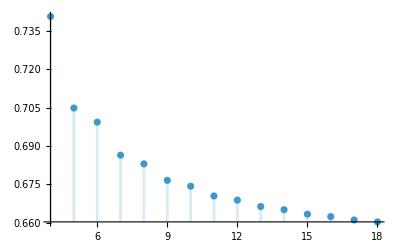

```mathematica
DiscretePlot[stairs2Mean[n], {n, 4, 18}]
```

```mathematica
(* Unfortunately, trying to compute and simplify stairs2Mean[n] does not work. I do not think there is a simple way to express this function; I tried several other methods including modifying orders of the summations, and this is the simplest version possible *)
```